# Ground state Hamiltonian for polar molecules

## Gabriel Patenotte 3/11/23

## Description

#### Overview

This code calculates the hyperfine and rotational states of the ground vib-electronic manifold. Each term in the molecular Hamiltonian is diagonal in a particular basis. I define several bases, such as ‘uncoupled’ or ‘fully coupled.’ Their quantum numbers are stored in basis variables called bX, where X = UC, SC, FC, etc. The list of states in that basis is stored in variables called lX. 

I  compute each Hamiltonian term in the basis that it is diagonal. Then, I apply a basis transformation matrix (in the code it is called X2Y, such as FC2UC) which expresses a Hamiltonian term that is diagonal in the fully coupled basis in the uncoupled basis. Lastly, I multiply each Hamiltonian term by molecular parameters and diagonalize the matrix to find the eigenstates.

Much of this code comes directly from Till’s notebook. I am more explicit about basis states and selection rules using particular quantum numbers. This code can scale to rotational states above N=1. Also, I include DC electric fields and allow the DC electric and magnetic fields to point in any direction.

#### Versions

V1: Ground state Hamiltonian for NaCs with elliptical polarization and magnetic fields
V2: Adding DC electric and magnetic fields in arbitrary directions, and constants for a range of molecules

## Setup

### Default options

Set plot preferences and turn off warning text for the parallel and main kernels.

```mathematica
SetOptions[Plot,BaseStyle->{FontFamily->"Arial",FontSize->20},TicksStyle->Directive[Black,10],Frame->True,FrameTicks->{Automatic,Automatic},ImagePadding->{{80,10},{80,10}},ImageSize->500,AxesLabel->{"",""},PlotStyle->Black]; 
ParallelEvaluate[Off[ClebschGordan::tri]];
ParallelEvaluate[Off[ClebschGordan::phy]];
Off[ClebschGordan::tri];
Off[ClebschGordan::phy];
```

### Helper functions

Shorthand functions used elsewhere in the notebook.

```mathematica
kp[a_,b_]:=KroneckerProduct[a,b](*shorthand Kronecker product*)
conj=Complex[a_,b_]->Complex[a,-b]; (*Replacement that gives the complex conjugate*)
J1dotJ2[J_,J1_,J2_]:=1/2(J(J+1)-J1(J1+1)-J2(J2+1))(*Dot product of two angular momenta*)
sphPlot[f_,options_:PlotStyle->Opacity[0.7]]:=SphericalPlot3D[f,{θ,0,π},{ϕ,0,2π},options,AxesLabel->{"X","Y","Z"},PlotRange->All]
```

### Constants and units

#### Definition

```mathematica
units=Association[cm->Quantity[1,"Centimeters"],um->Quantity[1,"Micrometers"],nm->Quantity[1,"Nanometers"],Hz->Quantity[1,"Hertz"],kHz->Quantity[1,"Kilohertz"],MHz->Quantity[1,"Megahertz"],GHz->Quantity[1,"Gigahertz"],THz->Quantity[1,"Terahertz"],icm->Quantity[1,("Centimeters")^-1],Debye->Quantity[1,"Debyes"],Gauss->Quantity[1,"Gauss"],mV->Quantity[1,"Millivolts"],V->Quantity[1,"Volts"]];
fundamental=Association[ϵ0->Quantity["Permittivity of free space"],ℏ->Quantity["ReducedPlanckConstant"],h->Quantity["PlanckConstant"],μB->Quantity["BohrMagneton"],μN->Quantity["NuclearMagneton"],a0->Quantity[1,"BohrRadius"]];

polarizability=Association[αpar->467.1,αperp->467.038,Δ->αpar-αperp,α0->(αpar+2αperp)/3]/.units/.fundamental;
nacs=Association[I1->3/2,I2->7/2,Bv->h 1.7396 GHz,eQq1->-h 97 kHz,eQq2->h 150 kHz,c1->h 14.2 Hz,c2->h 854.5 Hz,c3->h 105.6 Hz,c4->h 3941.8 Hz,gr->0,g1->1.478,g2->0.738,σ1->0.0006392,σ2->0.0062787,d0->4.6 Debye]/.units/.fundamental;
krb=Association[I1->3/2,I2->4,Bv->h 1.1139514 GHz,eQq1->h 452 kHz,eQq2->-h 1.308 MHz,c1->-h 24.1 Hz,c2->h 420.1 Hz,c3->h 0 Hz,c4->-h 2030.4 Hz,gr->0,g1->-0.324,g2->1.834,σ1->1321 10^-6,σ2->3469 10^-6,d0->1 Debye]/.units/.fundamental;
experiment=Association[θq->0,θh->0,U->h 1 MHz,B0->861 Gauss,E0->10^-5 mV/cm,θB->0,ϕB->0,θE->0,ϕE->0]/.units/.fundamental;
```

#### Default values

```mathematica
molecule=nacs;
constants=Association[{units,fundamental,polarizability,molecule,experiment}];
```

### Hilbert space

Defines the Hilbert state of the simulation. The number of states in a Hilbert space ℋ is given by nℋ. The states of the space are sℋ.

```mathematica
{Nmin,Nmax}={0,3};
{I1,I2}={I1,I2}/.molecule;
nℋ=Sum[(2I1+1)(2I2+1)(2N+1),{N,Nmin,Nmax}];
nℋI1=(2I1+1);
nℋI2=(2I2+1);
nℋI=(2I1+1)(2I2+1);
nℋN=Sum[(2N+1),{N,Nmin,Nmax}];
ℋ=IdentityMatrix[nℋ];
ℋI1=IdentityMatrix[nℋI1];
ℋI2=IdentityMatrix[nℋI2];
ℋI=IdentityMatrix[nℋI];
ℋN=IdentityMatrix[nℋN];
sℋ=Partition[ℋ,{nℋ,1}][[1]];
sℋI1=Partition[ℋI1,{nℋI1,1}][[1]];
sℋI2=Partition[ℋI2,{nℋI2,1}][[1]];
sℋI=Partition[ℋI,{nℋI,1}][[1]];
sℋN=Partition[ℋN,{nℋN,1}][[1]];
```

### Basis

#### Basis labels

```mathematica
bUC={"I1","mI1","I2","mI2","N","mN"};
bSC={"I1","I2","I","mI","N","mN"};
bFC={"I1","I2","I","N","F","mF"};
bF1={"I1","I2","mI2","N","F1","mF1"};
bF2={"I1","mI1","I2","N","F2","mF2"};
```

Sub-bases

```mathematica
bI1={"I1","mI1"};
bI2={"I2","mI2"};
bI={"I1","mI1","I2","mI2"};
bN={"N","mN"};
```

#### Basis states

```mathematica
lUC=Flatten[Table[bUC/.{"I1"->I1,"mI1"->mI1,"I2"->I2,"mI2"->mI2,"N"->N,"mN"->mN},{mI1,-I1,I1},{mI2,-I2,I2},{N,Nmin,Nmax},{mN,-N,N}],3];
lSC=Flatten[Table[bSC/.{"I1"->I1,"I2"->I2,"I"->I,"mI"->mI,"N"->N,"mN"->mN},{I,Abs[I1-I2],I1+I2},{mI,-I,I},{N,Nmin,Nmax},{mN,-N,N}],3];
lFC=Flatten[Table[bFC/.{"I1"->I1,"I2"->I2,"I"->I,"N"->N,"F"->F,"mF"->mF},{I,Abs[I1-I2],I1+I2},{N,Nmin,Nmax},{F,Abs[I-N],I+N},{mF,-F,F}],3];
lF1=Flatten[Table[bF1/.{"I1"->I1,"I2"->I2,"mI2"->mI2,"N"->N,"F1"->F1,"mF1"->mF1},{mI2,-I2,I2},{N,Nmin,Nmax},{F1,Abs[I1-N],I1+N},{mF1,-F1,F1}],3];
lF2=Flatten[Table[bF2/.{"I1"->I1,"mI1"->mI1,"I2"->I2,"N"->N,"F2"->F2,"mF2"->mF2},{mI1,-I1,I1},{N,Nmin,Nmax},{F2,Abs[I2-N],I2+N},{mF2,-F2,F2}],3];
```

Sub-labels

```mathematica
lI1=Table[bI1/.{"I1"->I1,"mI1"->mI1},{mI1,-I1,I1}];
lI2=Table[bI2/.{"I2"->I2,"mI2"->mI2},{mI2,-I2,I2}];
lI=Flatten[Table[bI/.{"I1"->I1,"mI1"->mI1,"I2"->I2,"mI2"->mI2},{mI1,-I1,I1},{mI2,-I2,I2}],1];
lN=Flatten[Table[bN/.{"N"->N,"mN"->mN},{N,Nmin,Nmax},{mN,-N,N}],1];
```

Check that the number of states matches the size of the Hilbert space for all bases.

```mathematica
(nℋ==Length[#])&/@{lUC,lSC,lFC,lF1,lF2}
```

{True,True,True,True,True}

Associate labels and states

```mathematica
b2l=AssociationThread[{bUC,bSC,bFC,bF1,bF2}->{lUC,lSC,lFC,lF1,lF2}];
```

#### Create basis transform matrix

```mathematica
b2b[bTo_,bFrom_,qTo_,qFrom_]:=With[{lTo=b2l[bTo],lFrom=b2l[bFrom],pFrom=Position[bFrom,#][[1,1]]&/@qFrom,pTo=Position[bTo,#][[1,1]]&/@qTo,pnTo=Position[bTo,#][[1,1]]&/@Intersection[bTo,bFrom],
pnFrom=Position[bFrom,#][[1,1]]&/@Intersection[bTo,bFrom]},Table[With[{to=lTo[[r]],from=lFrom[[c]]},If[to[[pnTo]]!=from[[pnFrom]],0,ClebschGordan[to[[pTo[[1;;2]]]],to[[pTo[[3;;4]]]],from[[pFrom]]]]],{r,Length[lTo]},{c,Length[lFrom]}]];
```

Basis transform matrices

```mathematica
SC2UC=b2b[bUC,bSC,{"I1","mI1","I2","mI2"},{"I","mI"}];
UC2SC=SC2UC†;
FC2SC=b2b[bSC,bFC,{"I","mI","N","mN"},{"F","mF"}];
SC2FC=FC2SC†;
F12UC=b2b[bUC,bF1,{"I1","mI1","N","mN"},{"F1","mF1"}];
UC2F1=F12UC†;
F22UC=b2b[bUC,bF2,{"I2","mI2","N","mN"},{"F2","mF2"}];
UC2F2=F22UC†;
F12FC=SC2FC.UC2SC.F12UC;
FC2F1=F12FC†;
F22FC=SC2FC.UC2SC.F22UC;
FC2F2=F22FC†;
UC2FC=SC2FC.UC2SC;
FC2UC=UC2FC†;
```

Check unitarity of basis transform matrix

```mathematica
ParallelMap[UnitaryMatrixQ[#]&,{SC2UC,FC2SC,F12UC,F22UC,F12FC,F22FC,UC2FC}]
```

{True,True,True,True,True,True,True}

#### Spherical harmonic bases

```mathematica
yUC=lUC[[All,Flatten[Position[bUC,#]&/@{"N","mN"}]]]/.{n_,mn_}->SphericalHarmonicY[n,mn,θ,ϕ];
yN=lN/.{n_,mn_}->SphericalHarmonicY[n,mn,θ,ϕ];
```

### Polarization

#### Jones vectors

```mathematica
qwp[θ_]=Exp[-(ⅈ π)/4]({{Cos[θ]^2+ⅈ Sin[θ]^2, (1-ⅈ) Sin[θ]Cos[θ]}, {(1-ⅈ) Sin[θ]Cos[θ], Sin[θ]^2+ⅈ Cos[θ]^2}});(*quarter waveplate Jones matrix*)
hwp[θ_]=Exp[-(ⅈ π)/2]({{Cos[θ]^2-Sin[θ]^2, 2Cos[θ]Sin[θ]}, {2Cos[θ]Sin[θ], Sin[θ]^2-Cos[θ]^2}});(*half waveplate Jones matrix*)
lpr[η_,θ_]=Exp[-(ⅈ η)/2]({{Cos[θ]^2+Exp[ⅈ η] Sin[θ]^2, (1-Exp[ⅈ η])Cos[θ]Sin[θ]}, {(1-Exp[ⅈ η])Cos[θ]Sin[θ], Sin[θ]^2+Exp[ⅈ η] Cos[θ]^2}});(*linear phase retarder Jones matrix*)

jH=({{1}, {0}});jV=({{0}, {1}});jL=1/(√2)({{1}, {ⅈ}});jR=1/(√2)({{1}, {-ⅈ}});(*Jones vectors for horizontal, vertical, LCP, and RCP light*)
jF[θh_,θq_]=FullSimplify[Flatten[hwp[θh].qwp[θq].jH],Assumptions->{0<=θh<2π,0<=θq<2π}];(*Jones vector seen by molecules*)
θd[θh_,θq_]:=ArcCos[Sin[2θh-θq]](*Angle between minor axis and array*)
```

```mathematica
pEllipse[θh_,θq_]=FullSimplify[ComplexExpand[Re[jF[θh,θq]Exp[-ⅈ t]]],Assumptions->{t>0,0<=θh<2π,0<=θq<2π}];
```

#### Polarizability

```mathematica
αMF=({{αperp, 0, 0}, {0, αperp, 0}, {0, 0, αpar}});(*Polarizability tensor in the molecular frame. It is diagonal for a linear molecule*)
Rx=RotationMatrix[θ,{1,0,0}];
Ry=RotationMatrix[θ,{0,1,0}];
Rz=RotationMatrix[ϕ,{0,0,1}];
αLF=Rzᵀ.Ryᵀ.αMF.Ry.Rz;
ϵ[θh_,θq_]={Append[jF[θh,θq],0]}ᵀ;(*Jones vector seen by the molecule, expressed in 3D coordinates*)
β[θ_,ϕ_]=-U/α0((ϵ[θh,θq]ᵀ/.Complex[a_,b_]->Complex[a,-b]).αLF.ϵ[θh,θq]-(αpar+2αperp)/3//FullSimplify)[[1,1]]/.(αpar-αperp)->Δ;
```

### Matrix elements

#### AC-Stark effect

```mathematica
srAC[{n1_,m1_},{n2_,m2_}]:=(n1==n2∨Abs[n1-n2]==2)∧(m1==m2∨Abs[m1-m2]==2)(*Selection rules for coupling between states*)
meAC[{Np_,Nmp_},{N_,Nm_}]:=If[srAC[{Np,Nmp},{N,Nm}],Integrate[SphericalHarmonicY[Np,Nmp,θ,ϕ]*SphericalHarmonicY[N,Nm,θ,ϕ]β[θ,ϕ] Sin[θ],{θ,0,π},{ϕ,0,2π}],0]
```

#### Stark effect

```mathematica
meE[{Nb_,Mb_},{Nk_,Mk_},q_:0]:=Sum[(-1)^mb √((2Nk+1)(2Nb+1))ThreeJSymbol[{Nb,-mb},{1,q},{Nk,mk}]ThreeJSymbol[{Nb,0},{1,0},{Nk,0}](WignerD[{Nb,mb,Mb},θE,ϕE]/.conj)WignerD[{Nk,mk,Mk},θE,ϕE],{mb,-Nb,Nb},{mk,-Nk,Nk}]
```

#### Zeeman effect

```mathematica
meZ[{Jb_,Mb_},{Jk_,Mk_}]:=Jb,Jk Sum[mk(WignerD[{Jb,mk,Mb},θB,ϕB]/.conj)WignerD[{Jk,mk,Mk},θB,ϕB],{mk,-Jk,Jk}]
```

### Hamiltonian

#### Spin-spin scalar coupling (I_1·I_2)

```mathematica
HI1I2SC=With[{p=Position[bSC,#][[1,1]]&/@{"I","I1","I2"}},DiagonalMatrix[Table[With[{II1I2=lSC[[n,p]]},
J1dotJ2@@II1I2],{n,1,nℋ}]]];
HI1I2UC=SC2UC.HI1I2SC.UC2SC;
```

#### Spin-rotation scalar coupling (N·I_(1,2))

```mathematica
HNI1F1=With[{p=Position[bF1,#][[1,1]]&/@{"F1","N","I1"}},DiagonalMatrix[Table[With[{F1NI1=lF1[[n,p]]},
J1dotJ2@@F1NI1],{n,1,nℋ}]]];
HNI1UC=F12UC.HNI1F1.UC2F1;
HNI2F2=With[{p=Position[bF2,#][[1,1]]&/@{"F2","N","I2"}},DiagonalMatrix[Table[With[{F2NI2=lF2[[n,p]]},
J1dotJ2@@F2NI2],{n,1,nℋ}]]];
HNI2UC=F22UC.HNI2F2.UC2F2;
```

#### Electric quadrupole coupling

```mathematica
HEQ1F1=With[{p=Position[bF1,#][[1,1]]&/@{"F1","N","I1"}},DiagonalMatrix[Table[With[{F1=lF1[[n,p[[1]]]],N=lF1[[n,p[[2]]]],I1=lF1[[n,p[[3]]]]},
-(3 J1dotJ2[F1,N,I1]^2+3/2 J1dotJ2[F1,N,I1]-I1(I1+1)N(N+1))/(2I1(2I1-1)(2N-1)(2N+3))]
,{n,1,nℋ}]]];
HEQ2F2=With[{p=Position[bF2,#][[1,1]]&/@{"F2","N","I2"}},DiagonalMatrix[Table[With[{F2=lF2[[n,p[[1]]]],N=lF2[[n,p[[2]]]],I2=lF2[[n,p[[3]]]]},
-(3 J1dotJ2[F2,N,I2]^2+3/2 J1dotJ2[F2,N,I2]-I2(I2+1)N(N+1))/(2I2(2I2-1)(2N-1)(2N+3))]
,{n,1,nℋ}]]];
HEQ1UC=F12UC.HEQ1F1.UC2F1;
HEQ2UC=F22UC.HEQ2F2.UC2F2;
```

#### Stark coupling

```mathematica
HacN=ParallelTable[meAC[lN[[i]],lN[[j]]],{i,1,Length[lN]},{j,1,Length[lN]}];
HSUC=With[{p=Position[bUC,#][[1,1]]&/@{"N","mN"},pn=Position[bUC,#][[1,1]]&/@{"mI1","mI2"}},ParallelTable[With[{bra=lUC[[i,p]],ket=lUC[[j,p]]},If[lUC[[i,pn]]==lUC[[j,pn]],meE[bra,ket],0]],{i,1,nℋ},{j,1,nℋ}]];
```

#### Zeeman coupling

```mathematica
HZNUC=With[{p=Position[bUC,#][[1,1]]&/@{"N","mN"},pn=Position[bUC,#][[1,1]]&/@{"mI1","mI2"}},ParallelTable[With[{bra=lUC[[i,p]],ket=lUC[[j,p]]},If[lUC[[i,pn]]==lUC[[j,pn]],meZ[bra,ket],0]],{i,1,nℋ},{j,1,nℋ}]];
HZI1UC=With[{p=Position[bUC,#][[1,1]]&/@{"I1","mI1"},pn=Position[bUC,#][[1,1]]&/@{"mN","mI2"}},ParallelTable[With[{bra=lUC[[i,p]],ket=lUC[[j,p]]},If[lUC[[i,pn]]==lUC[[j,pn]],meZ[bra,ket],0]],{i,1,nℋ},{j,1,nℋ}]];
HZI2UC=With[{p=Position[bUC,#][[1,1]]&/@{"I2","mI2"},pn=Position[bUC,#][[1,1]]&/@{"mI1","mN"}},ParallelTable[With[{bra=lUC[[i,p]],ket=lUC[[j,p]]},If[lUC[[i,pn]]==lUC[[j,pn]],meZ[bra,ket],0]],{i,1,nℋ},{j,1,nℋ}]];
```

#### Rotation

```mathematica
HNUC=With[{p=Position[bUC,"N"][[1,1]]},DiagonalMatrix[Table[
With[{N=lUC[[n,p]]},N(N+1)],{n,1,nℋ}]]];
```

#### Light shifts

```mathematica
HacUC=With[{p=Position[bUC,#][[1,1]]&/@{"N","mN"},pn=Position[bUC,#][[1,1]]&/@{"mI1","mI2"}},ParallelTable[With[{to=Position[lN,lUC[[i,p]]][[1,1]],from=Position[lN,lUC[[j,p]]][[1,1]]},If[lUC[[i,pn]]==lUC[[j,pn]],HacN[[to,from]],0]],{i,1,nℋ},{j,1,nℋ}]];
```

#### Dipole transitions

```mathematica
He1UC=Table[With[{p=Position[bUC,#][[1,1]]&/@{"N","mN"},pn=Position[bUC,#][[1,1]]&/@{"mI1","mI2"}},ParallelTable[With[{to=lUC[[i,p]],from=lUC[[j,p]]},If[lUC[[i,pn]]==lUC[[j,pn]],meE[to,from,q]/.{θE->0,ϕE->0},0]],{i,1,nℋ},{j,1,nℋ}]],{q,-1,1}];
```

#### Total Hamiltonian

```mathematica
HUC=Bv HNUC+c4 HI1I2UC+c1 HNI1UC+c2 HNI2UC+eQq1 HEQ1UC+eQq2 HEQ2UC-gr μN B0 HZNUC-g1 μN(1-σ1)B0 HZI1UC-g2 μN(1-σ2)B0 HZI2UC+HacUC+d0 E0 HSUC;
```

### Eigenstates

#### Find states

```mathematica
findUC[rep_]:=With[{labels=rep[[All,1]],numbers=rep[[All,2]]},Flatten[Position[lUC[[All,Flatten[labels/.PositionIndex[bUC]]]],numbers]]]
findSC[rep_]:=With[{labels=rep[[All,1]],numbers=rep[[All,2]]},Flatten[Position[lSC[[All,Flatten[labels/.PositionIndex[bSC]]]],numbers]]]
findEigen[rep_]:=Module[{pos,eigs},pos=findUC[rep];eigs=OrderingBy[eUC[[2,All,pos]],Total[Abs[#]^2]&][[-Length[pos];;-1]];eigs[[Ordering@eUC[[1,eigs]]]]]
findEigenSC[rep_]:=Module[{pos,eigs},pos=findSC[rep];eigs=OrderingBy[eSC[[2,All,pos]],Total[Abs[#]^2]&][[-Length[pos];;-1]];eigs[[Ordering@eSC[[1,eigs]]]]]
```

#### Decompose states

```mathematica
sUCp[n_,f_:0.1]:=Module[{sS,sP},sS=SortBy[Select[eUC[[2]][[n]],Abs[#]^2>=f&],Abs];
sP=Position[eUC[[2]][[n]],#][[1,1]]&/@sS;
Transpose@{Abs[#]^2&/@sS,lUC[[sP]]}]
sSCp[n_,f_:0.1]:=Module[{sS,sP},sS=SortBy[Select[eSC[[2]][[n]],Abs[#]^2>=f&],Abs];
sP=Position[eSC[[2]][[n]],#][[1,1]]&/@sS;
Transpose@{Abs[#]^2&/@sS,lSC[[sP]]}]
```

### Operators

Create the J_(n̂) operator with n̂ at an angle θ and ϕ from Ẑ.

```mathematica
Jn[J_,θ_:0,ϕ_:0]:=Table[Sum[(WignerD[{J,m,N},θ,ϕ]/.conj)WignerD[{J,m,M},θ,ϕ]m,{m,-J,J}],{N,-J,J},{M,-J,J}]
```

### Density matrices

```mathematica
pos2ρ[pos_]:=Module[{ψ,ρIN,ρI,ρN,ρI1,ρI2},
ψ={eUC[[2,pos]]}ᵀ;
ρIN=ψ.ψ†;
ρI=Sum[kp[ℋI,sℋN[[j]]ᵀ].ρIN.kp[ℋI,sℋN[[j]]],{j,1,nℋN}];
ρN=Sum[kp[sℋI[[j]]ᵀ,ℋN].ρIN.kp[sℋI[[j]],ℋN],{j,1,nℋI}];
ρI1=Sum[kp[ℋI1,sℋI2[[j]]ᵀ].ρI.kp[ℋI1,sℋI2[[j]]],{j,1,nℋI2}];
ρI2=Sum[kp[sℋI1[[j]]ᵀ,ℋI2].ρI.kp[sℋI1[[j]],ℋI2],{j,1,nℋI1}];
{ρI,ρN,ρI1,ρI2}]
pos2e[pos_]:=Module[{ψ,ρIN,ρI,ρN,ρI1,ρI2,eI,eN,eI1,eI2},
ψ={eUC[[2,pos]]}ᵀ;
ρIN=ψ.ψ†;
ρI=Sum[kp[ℋI,sℋN[[j]]ᵀ].ρIN.kp[ℋI,sℋN[[j]]],{j,1,nℋN}];
ρN=Sum[kp[sℋI[[j]]ᵀ,ℋN].ρIN.kp[sℋI[[j]],ℋN],{j,1,nℋI}];
ρI1=Sum[kp[ℋI1,sℋI2[[j]]ᵀ].ρI.kp[ℋI1,sℋI2[[j]]],{j,1,nℋI2}];
ρI2=Sum[kp[sℋI1[[j]]ᵀ,ℋI2].ρI.kp[sℋI1[[j]],ℋI2],{j,1,nℋI1}];
eI=Eigensystem[ρI];
eI=Sort[eIᵀ]ᵀ;
eN=Eigensystem[ρN];
eN=Sort[eNᵀ]ᵀ;
eI1=Eigensystem[ρI1];
eI1=Sort[eI1ᵀ]ᵀ;
eI2=Eigensystem[ρI2];
eI2=Sort[eI2ᵀ]ᵀ;
{eI,eN,eI1,eI2}]
```

### Visualize

#### N states

```mathematica
pos2sph[pos_]:=Module[{ψ,ρIN,ρI,ρN,eI,eN},
ψ={eUC[[2,pos]]}ᵀ;
ρIN=ψ.ψ†;
ρI=Sum[kp[ℋI,sℋN[[j]]ᵀ].ρIN.kp[ℋI,sℋN[[j]]],{j,1,nℋN}];
ρN=Sum[kp[sℋI[[j]]ᵀ,ℋN].ρIN.kp[sℋI[[j]],ℋN],{j,1,nℋI}];
eI=Eigensystem[ρI];
eI=Sort[eIᵀ]ᵀ;
eN=Eigensystem[ρN];
eN=Sort[eNᵀ]ᵀ;
SphericalPlot3D[Abs[eN[[2,4]].yN]^2,{θ,0,π},{ϕ,0,2π},PlotRange->All]]
```

## Test

```mathematica
func[f_]:=Module[{H,e,p,omegas,ff},
H=Chop[N[QuantityMagnitude[UnitConvert[(HUC/h/.B0->f Quantity["Gauss"])//.constants]]]];
e=Chop[Sort[Eigensystem[H]ᵀ]ᵀ,10^-9];
p={36,37,38};
omegas=Mean[Table[With[{ψ={e[[2,p[[q]]]]}ᵀ},
ff=Total[Table[({e[[2,#]]}.He1UC[[q]].ψ)[[1,1]],{q,1,3}]^2]&/@{2,3}],{q,1,3}]];
omegas[[1]]/omegas[[2]]]
```

```mathematica
func[800]
```

2387.7

```mathematica
sUCp[3,10^-10]
```

{{1.38274×10^-10,{3/2,1/2,7/2,5/2,1,0}},{2.31885×10^-9,{3/2,-1/2,7/2,7/2,0,0}},{2.35185×10^-7,{3/2,3/2,7/2,3/2,2,0}},{2.11258×10^-6,{3/2,3/2,7/2,3/2,1,0}},{0.00010877,{3/2,1/2,7/2,5/2,0,0}},{0.999889,{3/2,3/2,7/2,3/2,0,0}}}

```mathematica
omegas[[1]]/omegas[[2]]
```

2387.7

```mathematica
func[800]
```

{3.47673×10^9,3.47675×10^9,3.47675×10^9}

```mathematica
func[50]
```

{3.47904×10^9,3.47905×10^9,3.47906×10^9}

```mathematica
tab=ParallelTable[func[bb0],{bb0,50,850,50}]
```

{1.41835,20.7789,58.0761,114.967,191.943,289.203,406.84,544.908,703.44,882.461,1081.99,1302.04,1542.62,1803.75,2085.44,2387.7,2710.54}

```mathematica
tab0=ParallelTable[func[bb0],{bb0,50,850,50}]
```

$Aborted

```mathematica
tab[[1]]-tab[[1,2]]
```

{-12659.6,0.,1140.78}

```mathematica
tab[[1]]
```

1.41835

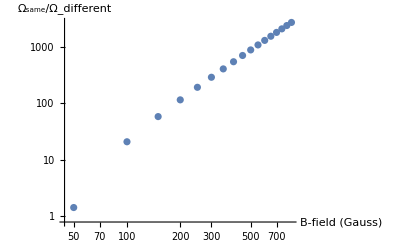

```mathematica
ListLogLogPlot[Transpose@{Range[50,850,50],tab},AxesLabel->{"B-field (Gauss)","Ω_same/Ω_different"},PlotRange->All]
```

```mathematica
HUCn=Chop[N[QuantityMagnitude[UnitConvert[HUC/h/.B0->860 Gauss//.constants]]]];
```

```mathematica
eUC=Chop[Sort[Eigensystem[HUCn]ᵀ]ᵀ,10^-9];
p0=findEigen[{"N"->0,"mI1"->3/2,"mI2"->5/2}]
p1=findEigen[{"N"->1,"mI1"->3/2,"mI2"->5/2}]
p01=findEigen[{"N"->0,"mI1"->3/2}]
```

{2}

{36,37,38}

{1,2,3,5,7,10,13,17}

```mathematica
Table[With[{ψ={eUC[[2,p1[[q]]]]}ᵀ},
f=Total[Table[({eUC[[2,#]]}.He1UC[[q]].ψ)[[1,1]],{q,1,3}]^2]&/@p01//ScientificForm],{q,1,3}]//TableForm
```

{5.98819×10^-5,3.32937×10^-1,1.61043×10^-4,5.01451×10^-5,9.25374×10^-15,1.80267×10^-13,0.,0.}
{1.24331×10^-4,3.33009×10^-1,7.72784×10^-5,2.33398×10^-5,4.5304×10^-15,8.7774×10^-14,0.,0.}
{2.52634×10^-4,3.33056×10^-1,1.21346×10^-4,2.06087×10^-12,3.36162×10^-12,0.,0.,0.}

```mathematica
(2.5 10^-1)/(2.87 10^-2)
```

8.7108

```mathematica
(3.32 10^-1)/(1.6 10^-4)
```

2075.

```mathematica
eUC[[1,p01]]-eUC[[1,p0]][[1]]
```

{-475737.,0.,475610.,951092.,1.42645×10^6,1.90167×10^6,2.37676×10^6,2.85172×10^6}

```mathematica
eUC[[1,p1]]-eUC[[1,p1[[2]]]]
```

{-14338.5,0.,3834.88}

```mathematica
sUCp[#,0.01]&/@p1//TableForm
```

0.310972 |  |  |  |  | 
3/2 | 3/2 | 7/2 | 5/2 | 1 | 1 | 0.687685 |  |  |  |  | 
3/2 | 3/2 | 7/2 | 5/2 | 1 | -1
0.310768 |  |  |  |  | 
3/2 | 3/2 | 7/2 | 5/2 | 1 | -1 | 0.688121 |  |  |  |  | 
3/2 | 3/2 | 7/2 | 5/2 | 1 | 1
0.99842 |  |  |  |  | 
3/2 | 3/2 | 7/2 | 5/2 | 1 | 0 |

## Evaluate

### Diagonalize the Hamiltonian

#### Hamiltonian with default replacements

```mathematica
(*rep={U->10 h MHz,θB->0,ϕB->0,B0->200 Gauss,E0->0 V/cm,θE->0,ϕE->0,Δ->0};*)
HUCn=QuantityMagnitude[UnitConvert[HUC/h//.constants]];
(*HFCn=UC2FC.HUCn.FC2UC;
HSCn=UC2SC.HUCn.SC2UC;*)
```

#### Eigensystem of the Hamiltonian

```mathematica
eUC=Sort[Eigensystem[HUCn]ᵀ]ᵀ;
(*eSC=Sort[Eigensystem[HSCn]ᵀ]ᵀ;
eFC=Sort[Eigensystem[HFCn]ᵀ]ᵀ;*)
```

```mathematica
n3=findEigen[{"N"->3,"mI1"->3/2,"mI2"->5/2}];
n2=findEigen[{"N"->2,"mI1"->3/2,"mI2"->5/2}];
n1=findEigen[{"N"->1,"mI1"->3/2,"mI2"->5/2}];
n0=findEigen[{"N"->0,"mI1"->3/2,"mI2"->5/2}];
```

```mathematica
sUCp[#]&/@n2
```

{{{0.998265,{3/2,3/2,7/2,5/2,2,-1}}},{{0.999262,{3/2,3/2,7/2,5/2,2,0}}},{{0.999188,{3/2,3/2,7/2,5/2,2,1}}},{{0.998434,{3/2,3/2,7/2,5/2,2,-2}}},{{0.999188,{3/2,3/2,7/2,5/2,2,2}}}}

```mathematica
eUC[[1,n3]]-eUC[[1,n3[[5]]]]
eUC[[1,n2]]-eUC[[1,n2[[3]]]]
eUC[[1,n1]]-eUC[[1,n1[[2]]]]
```

{-4110.96,-3063.75,-2943.79,-125.019,0.,5523.22,13612.1}

{-3947.06,-3922.65,0.,158.821,9689.81}

{-6149.15,0.,5418.37}

#### Spin coupled plot for Annie

```mathematica
tab=Flatten[Table[Union[sSCp[i,10^-1][[All,2]][[All,4]]],{i,1,nℋ}]]
```

{5,4,3,4,2,3,1,3,2,0,1,2,-1,2,0,1,-2,-1,1,0,-2,0,-1,-3,-2,-1,-3,-2,-4,-3,-4,-5,5,5,5,4,4,4,3,4,4,3,3,4,2,3,3,2,2,3,1,3,3,2,1,1,2,2,3,0,0,0,2,2,1,1,1,2,-1,-1,-1,2,2,0,2,0,0,1,1,1,-2,-2,-2,1,-1,-1,-1,1,0,1,0,0,-2,0,-2,-1,-2,-1,-1,0,0,-3,-3,-1,-2,-2,-2,-3,-1,-1,-2,-3,-3,-3,-2,-2,-4,-4,-3,-3,-3,-4,-4,-4,-4,-5,-5,-5}

```mathematica
p0=findEigen[{"N"->0,"mI1"->3/2,"mI2"->5/2}]
p1=findEigen[{"N"->1,"mI1"->3/2,"mI2"->5/2}]
```

{2}

{36,37,38}

```mathematica
pcl=ConstantArray[Black,nℋ];
pcl[[p0]]=ColorData[3,2];
pcl[[p1]]=ColorData[3,6];
(*pcl[[p2]]=ColorData[3,4];*)
```

```mathematica
pn0=Transpose@{tab[[1;;32]],10^-6 eFC[[1,1;;32]]};
pn1=Transpose@{tab[[33;;128]],(eFC[[1,33;;128]]-QuantityMagnitude[UnitConvert[2 Bv/h/.constants]])/10^6};
(*pn2=Transpose@{tab[[129;;nℋ]],(eFC[[1,129;;nℋ]]-QuantityMagnitude[UnitConvert[6 Bv/h/.constants]])/10^6};*)
```

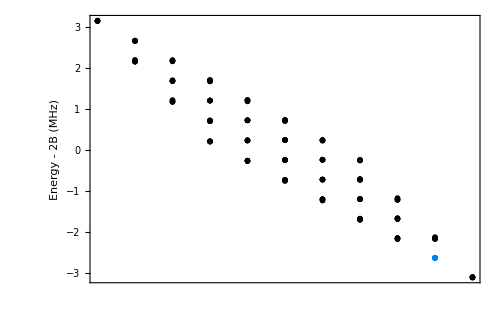

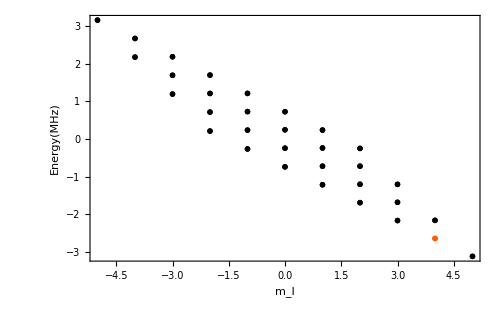

```mathematica
SetOptions[ListPlot,BaseStyle->{FontFamily->"Arial",FontSize->16},TicksStyle->Directive[Black,10],Frame->True,Joined->False,FrameTicks->{Automatic,Automatic},ImagePadding->{{60,10},{60,10}},ImageSize->500,AxesLabel->{"",""},PlotMarkers->{"—",25},PlotStyle->Black]; 
(*l2=ListPlot[{#}&/@pn2,FrameLabel->{"","Energy - 6B (MHz)"},PlotStyle->pcl[[129;;nℋ]],FrameTicks->{None,Automatic}]*)
l1=ListPlot[{#}&/@pn1,FrameLabel->{"","Energy - 2B (MHz)"},PlotStyle->pcl[[33;;128]],FrameTicks->{None,Automatic}]
l0=ListPlot[{#}&/@pn0,FrameLabel->{"m_I","Energy(MHz)"},PlotStyle->pcl[[1;;32]]]
```

#### Find initial state

```mathematica
p0=findEigen[{"mI1"->3/2,"mI2"->5/2,"N"->0}];
p1=findEigen[{"mI1"->3/2,"mI2"->5/2,"N"->1}];
e0=eUC[[All,p0]];
bUC
TableForm[ScientificForm/@sUCp[p1[[1]],.0001]];
```

{I1,mI1,I2,mI2,N,mN}

```mathematica
ψ={eUC[[2,p1[[]]]]}ᵀ;
f=Table[Table[Chop[{eUC[[2,n]]}.He1UC[[q+2]].ψ][[1,1]],{n,1,32}],{q,-1,1}];
ListPlot[Abs[f]^2,PlotRange->All,PlotLegends->{"-1","0","1"},PlotMarkers->Automatic]
```

Dot::dotsh: Tensors {{0.,0.,0.,-1.12145×10^-197,-1.70293×10^-197,0.,0.,-3.99428×10^-118,8.02629×10^-119,0.,«118»}} and {{{0.,0.,0.,0.,0.,0.,0.,3.3341×10^-34,4.65655×10^-42,0.,«118»}},{{0.,0.,0.,0.,0.,0.,0.,-9.66719×10^-23,-1.51679×10^-27,0.,«118»}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«118»}}} have incompatible shapes.

Dot::dotsh: Tensors {{0,0,0,0,0,0,0,0,0,0,«118»}} and {{{0,0,0,0,0,0,0,0,0,0,«118»}},{{0,0,0,0,0,0,0,0,0,0,«118»}},{{0,0,0,0,0,0,0,0,0,0,«118»}}} have incompatible shapes.

Dot::dotsh: Tensors {{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«118»}} and {{{0.,0.,0.,0.,0.,0.,0.,3.3341×10^-34,4.65655×10^-42,0.,«118»}},{{0.,0.,0.,0.,0.,0.,0.,-9.66719×10^-23,-1.51679×10^-27,0.,«118»}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«118»}}} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

-Graphics-

```mathematica
pN1=findEigen[{"N"->1}];
```

```mathematica
pN0=findEigen[{"N"->0}];
```

```mathematica
ψ0={eUC[[2,p1[[2]]]]}ᵀ;
d021=ParallelTable[Abs[({eUC[[2,i]]}.He1UC[[q+2]].ψ0)[[1,1]]]^2,{i,1,Length[pN0]},{q,1,1}];
```

```mathematica
pt=Ordering[{Total/@d021,pN0}ᵀ][[-3;;-1]];
```

```mathematica
ψ0={eUC[[2,p0[[1]]]]}ᵀ;
Hm=10^6 He1UC[[3]]+DiagonalMatrix[Join[ConstantArray[0,32],ConstantArray[-deltaE,96]]]+HUCn;
ParallelTable[Abs[ψ0†.MatrixExp[-ⅈ Hm 10^-6 t].ψ0]^2,{t,0.1,10}]
```

```mathematica
deltaE=eUC[[1,p1[[2]]]]-eUC[[1,p0[[1]]]]
Hm=10^6 He1UC[[3]]+DiagonalMatrix[Join[ConstantArray[0,32],ConstantArray[-deltaE,96]]]+HUCn;
```

3.47921×10^9+0. ⅈ

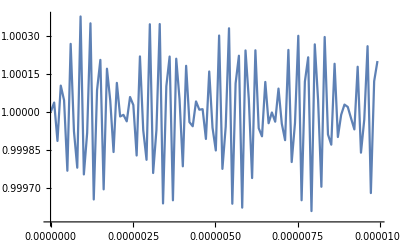

```mathematica
tab=ParallelTable[{t,(Abs[{eUC[[2,p0[[1]]]]}.MatrixExp[-ⅈ Hm t].{eUC[[2,p0[[1]]]]}ᵀ]^2)[[1,1]]},{t,10^-8,10^-5,10^-7}];
ListPlot[tab,Joined->True,PlotRange->All]
```

```mathematica
coupledStates[rep_,init_:{"mI1"->3/2,"mI2"->5/2,"N"->0}]:=Module[{HUCn,eUC,p0,e0,pN1,ψ0,ds,p1},HUCn=QuantityMagnitude[UnitConvert[HUC/h/.rep//.constants]];eUC=Sort[Eigensystem[HUCn]ᵀ]ᵀ;
p0=findEigen[init];
e0=eUC[[All,p0]];
pN1=findEigen[{"N"->1}];
ψ0=e0[[2]]ᵀ;
ds=Table[Chop[Abs[({eUC[[2,pN1[[i]]]]}.He1UC[[q+2]].ψ0)[[1,1]]]^2],{i,1,Length[pN1]},{q,-1,1}];
p1=32+Ordering[{Total/@ds,pN1}ᵀ][[-3;;-1]];
Sort[eUC[[1,#]]&/@p1]
]
```

```mathematica
scan[func_,reps_]:=ParallelTable[func[rep],{rep,reps}]
reps=Table[{B->x Gauss},{x,0.1,800,100}];
res=scanVariable[reps]ᵀ;
```

```mathematica
ListPlot[res[[2]]-res[[2,1]],Joined->True,PlotRange->All]
```

Part::partw: Part 2 of Transpose[scanVariable[{{B→0.1 Gauss},{B→100.1 Gauss},{B→200.1 Gauss},{B→300.1 Gauss},{B→400.1 Gauss},{B→500.1 Gauss},{B→600.1 Gauss},{B→700.1 Gauss}}]] does not exist.

ListPlot::lpn: Transpose[scanVariable[{{B→Times[«2»]},{B→Times[«2»]},{B→Times[«2»]},{B→Times[«2»]},{B→Times[«2»]},{B→Times[«2»]},{B→Times[«2»]},{B→Times[«2»]}}]]⟦2⟧-1. Transpose[scanVariable[{{Rule[«2»]},{Rule[«2»]},{Rule[«2»]},{Rule[«2»]},{Rule[«2»]},{Rule[«2»]},{Rule[«2»]},{Rule[«2»]}}]]⟦2,1⟧ is not a list of numbers or pairs of numbers.

ListPlot[Transpose[scanVariable[{{B→0.1 Gauss},{B→100.1 Gauss},{B→200.1 Gauss},{B→300.1 Gauss},{B→400.1 Gauss},{B→500.1 Gauss},{B→600.1 Gauss},{B→700.1 Gauss}}]]⟦2⟧-Transpose[scanVariable[{{B→0.1 Gauss},{B→100.1 Gauss},{B→200.1 Gauss},{B→300.1 Gauss},{B→400.1 Gauss},{B→500.1 Gauss},{B→600.1 Gauss},{B→700.1 Gauss}}]]⟦2,1⟧,Joined→True,PlotRange→All]

#### Continue

```mathematica
pN0=findEigen[{"mI1"->3/2,"mI2"->5/2,"N"->0}];
pN1=findEigen[{"mI1"->3/2,"mI2"->5/2,"N"->1}]
```

{36,37,38}

```mathematica
bUC
TableForm[sUCp[#]ᵀ&/@pN0]
TableForm[sUCp[#]ᵀ&/@pN1]
```

{I1,mI1,I2,mI2,N,mN}

0.999646 | 3/2 | 3/2 | 7/2 | 5/2 | 0 | 0

0.498612
0.500908 | 3/2 | 3/2 | 7/2 | 5/2 | 1 | 1
3/2 | 3/2 | 7/2 | 5/2 | 1 | -1
0.49521
0.496683 | 3/2 | 3/2 | 7/2 | 5/2 | 1 | -1
3/2 | 3/2 | 7/2 | 5/2 | 1 | 1
0.999584 | 3/2 | 3/2 | 7/2 | 5/2 | 1 | 0

```mathematica
Chop[{eUC[[2,pN1[[1]]]]}.He1UC.{eUC[[2,pN0[[1]]]]}ᵀ,10^-6]
```

{{0,-0.0022004,-0.0000106305,-0.00231011,0,-0.00985377,0,-0.0102129,0,-0.0290172,0.000105138,-0.0297304,0,-0.0639777,0.000370222,-0.0648979,0,-0.10976,0.000719027,-0.110413,0,-0.146523,0.00086589,-0.14643,0,-0.146455,0.000566153,-0.145679,0,-0.0962672,0.0000415291,-0.0954978,0,-0.00377061,-0.0000345999,-0.00399178,0,-0.0168318,-0.0000722543,-0.0175962,0,-0.049394,-0.0000375223,-0.0510593,0,-0.108494,0.000151843,-0.11106,0,-0.185369,0.000402295,-0.188211,0,-0.246359,0.000381077,-0.248534,0,-0.245062,-0.000114454,-0.246093,0,-0.160249,-0.000618354,-0.160491,0,-0.00150924,-2.26727×10^-6,-0.00162662,0,-0.00657305,0.0000240171,-0.00700546,0,-0.0187628,0.000140393,-0.0198033,0,-0.0399526,0.000398313,-0.0418254,0,-0.06592,0.000732587,-0.0685659,0,-0.0842283,0.000920148,-0.0872025,0,-0.0801369,0.000755613,-0.0827365,0,-0.0498165,0.000332278,-0.0513883,0,0.00347976,0.0000369466,0.00360464,0,0.015856,0.0000891799,0.0162087,0,0.0475656,0.0000938914,0.0480506,0,0.106958,-0.0000327161,0.106944,0,0.187357,-0.000224033,0.185743,0,0.255664,-0.000175188,0.25179,0,0.261513,0.000320913,0.256374,0,0.176108,0.000798433,0.172227}}.He1UC.{{-0.00301328},{0},{-1.8873×10^-6},{0},{-0.0137352},{0},{-8.59276×10^-6},{0},{-0.0409852},{0},{-0.0000256104},{0},{-0.0911532},{0},{-0.0000568912},{0},{-0.157029},{0},{-0.000097888},{0},{-0.209532},{0},{-0.000130458},{0},{-0.208388},{0},{-0.000129585},{0},{-0.135673},{0},{-0.0000842616},{0},{-0.00513427},{0},{-3.23099×10^-6},{0},{-0.0233079},{0},{-0.0000146384},{0},{-0.0692631},{0},{-0.0000434115},{0},{-0.1534},{0},{-0.0000959446},{0},{-0.263137},{0},{-0.00016423},{0},{-0.349602},{0},{-0.000217719},{0},{-0.346168},{0},{-0.000215101},{0},{-0.224373},{0},{-0.000139102},{0},{-0.00212819},{0},{-1.38583×10^-6},{0},{-0.00937111},{0},{-6.05983×10^-6},{0},{-0.0269689},{0},{-0.0000173069},{0},{-0.0577453},{0},{-0.0000367483},{0},{-0.0955855},{0},{-0.0000602704},{0},{-0.122295},{0},{-0.000076327},{0},{-0.116348},{0},{-0.0000717926},{0},{-0.0722749},{0},{-0.0000440309},{0},{0.00463644},{0},{2.8246×10^-6},{0},{0.0216283},{0},{0.0000132348},{0},{0.0660293},{0},{0.0000405772},{0},{0.150205},{0},{0.0000926848},{0},{0.264595},{0},{0.000163914},{0},{0.360938},{0},{0.000224448},{0},{0.366885},{0},{0.000228982},{0},{0.244075},{0},{0.000152871},{0}}

```mathematica
bvec=.3{Sin[θB]Cos[ϕB],Sin[θB]Sin[ϕB],Cos[θB]}/.rep//.constants;
evec=.3{Sin[θE]Cos[ϕE],Sin[θE]Sin[ϕE],Cos[θE]}/.rep//.constants;
sphs=ParallelTable[pos2sph[i],{i,n1pos}];
Show[sphs,Graphics3D[{Arrow[{{0,0,0},bvec}],Red,Arrow[{{0,0,0},evec}]}]]
```

ParallelTable::iterb: Iterator {i,n1pos} does not have appropriate bounds.

ParallelTable::nopar1: ParallelTable[pos2sph[i],{i,n1pos}] cannot be parallelized; proceeding with sequential evaluation.

Table::iterb: Iterator {i,n1pos} does not have appropriate bounds.

Show::gcomb: Could not combine the graphics objects in Show[Table[pos2sph[i],{i,n1pos}],].

Show[Table[pos2sph[i],{i,n1pos}],-Graphics3D-]

```mathematica
pos2e[pN1[[1]]][[2,2,-1]][[2;;4]]
```

{-0.829777,9.02709×10^-23,-0.558095}

```mathematica
pos2e[pN1[[3]]][[2,2,-1]][[2;;4]]
```

{9.85015×10^-22,1.,-3.49112×10^-20}

```mathematica
pN1
```

{36,37,38}

```mathematica
ψ={pos2e[pN1[[1]]][[2,2,-1]][[2;;4]]}ᵀ;
val=.;val=(ψᵀ.Jn[1,θ,ϕ].ψ)[[1,1]];
SphericalPlot3D[Abs[val]^2,{θ,0,π},{ϕ,0,2π}]
```

-Graphics3D-

-Graphics3D-

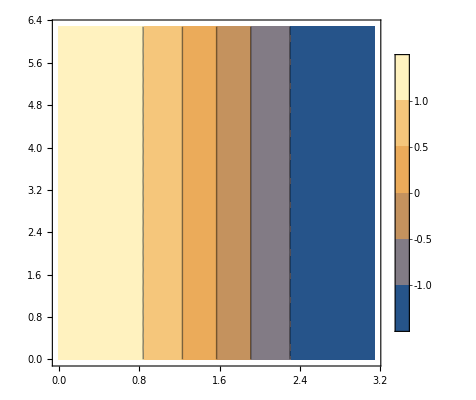

```mathematica
ContourPlot[val,{θ,0,π},{ϕ,0,2π},PlotLegends->Automatic]
```

```mathematica
val1=Re[val[[1,1]]];
```

```mathematica
NMaximize[val1,{θ,ϕ}]
```

{0.499962,{θ→1.04726,ϕ→3.70269×10^-8}}

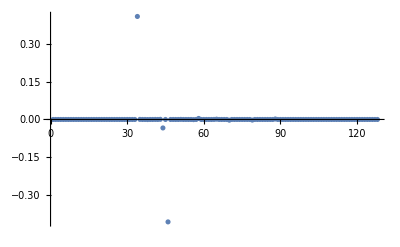

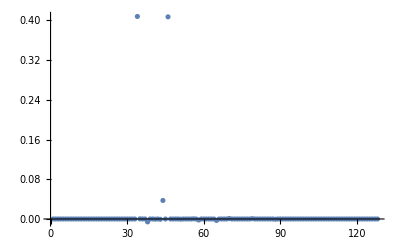

```mathematica
ψ={eUC[[2,pN0[[1]]]]}ᵀ;
f=Table[Chop[{eUC[[2,n]]}.He1UC[-1].ψ][[1,1]],{n,1,128}];
ListPlot[f,PlotRange->All]
```

```mathematica
sUCp[2,10^-2]
```

{{0.999646,{3/2,3/2,7/2,5/2,0,0}}}

```mathematica
pN1
```

{34,46,72}

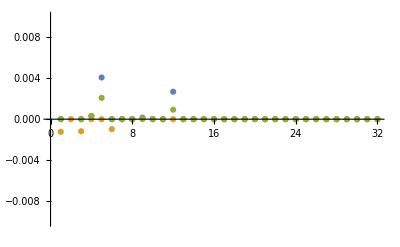

```mathematica
ψ={eUC[[2,pN1[[1]]]]}ᵀ;
f=Table[Table[Chop[{eUC[[2,n]]}.He1UC[q].ψ][[1,1]],{n,1,32}],{q,-1,1}];
ListPlot[f,PlotRange->{-.01,0.01}]
```